```mathematica
e=N[UnitConvert[Quantity["ElementaryCharge"]]]
```

1.60218×10^-19 s A

```mathematica
Quantity[1 10^-12 ,"s A"]/e
```

6.24151×10^6

1pC is 6M electrons

n is not number of electrons but number density. We have 1 pC with waist 25um, lets say bunch is 1 ps long = 300 um

```mathematica
n=(Quantity[1 10^-12 ,"s A"]/e)/Quantity[(π((25/2)10^-6)^2 300 10^-6),"m*m*m"]
```

4.23837×10^19 per meter^3

```mathematica
me=UnitConvert[Quantity["ElectronMass"]]
```

9.1093837×10^-31 kg

```mathematica
ϵ0=UnitConvert[Quantity["VacuumPermittivity"]]
```

8.85418781×10^-12 s^4 A^2/(kg m^3)

Plasma frequency is

```mathematica
Subscript[Ω, p][n_]:= Sqrt[(e^2 n)/(ϵ0 me)]
```

```mathematica
Subscript[Ω, p][n]
```

3.67274×10^11 per second

```mathematica
c=UnitConvert[Quantity["SpeedOfLight"]]
```

299792458 m/s

inverse relativistic plasma wavenumber is

```mathematica
Subscript[k, pinv][γ_,n_]:=(c γ^3)/(Subscript[Ω, p][n])
```

Energy is 7.2 MeV so γ is

```mathematica
(7.2+0.511)/0.511
```

15.09

```mathematica
Subscript[k, pinv][15,n]
```

2.75489 m

but this is for an average density bunch. If we microbunch at 13.5 nm then consider a comb of interval 13.5 / 2, there are 22222 intervals. Half are filled with charge so we split our 1 pc into 10000. Then for one microbunch we have

```mathematica
n=((Quantity[1 10^-12 ,"s A"]/e)/10000)/Quantity[(π((25/2)10^-6)^2 (13.5/2) 10^-9),"m*m*m"]
```

1.88372×10^20 per meter^3

and k is then

```mathematica
Subscript[k, pinv][(7.2+0.511)/0.511,n]
```

1.33043 m

So it looks like it is plausible that a microbunch can survive over a propagation of ~ 1m

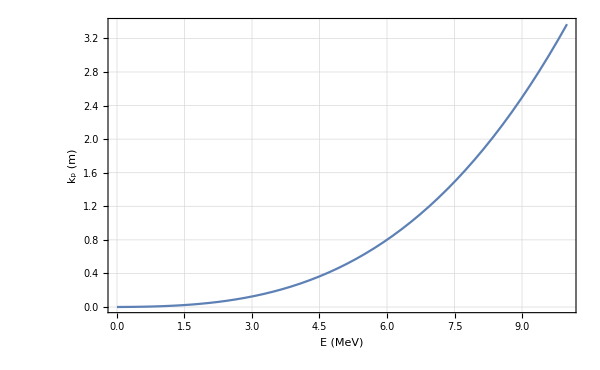

```mathematica
plot1=Plot[Subscript[k, pinv][(E+0.511)/0.511,n],{E,0,10},Frame->True,GridLines->Automatic,LabelStyle->Black,BaseStyle->{FontFamily->"Helvetica",Bold,FontSize->14},FrameLabel->{"E (MeV)","k_p (m)","",""},PlotRange->All,ImageSize->600]
```

```mathematica
NotebookDirectory[]
```

D:\ASML\2020 ICS EUV\

```mathematica
Export[NotebookDirectory[]<>"euvics.png",plot1]
```

D:\ASML\2020 ICS EUV\euvics.png